```mathematica
A. Lagrange Formula
```

```mathematica
1.
```

```mathematica
Density = 6.50600; (* g/cm^3 *)
Energy0 = 0.8; (* MeV *)
Energy1 = 1.0; (* MeV *)
MassAttenuation0 = 6.571*10^-2; (* cm^2/g *)
MassAttenuation1=5.810*10^-2; (* cm^2/g *)
LinearAttenuation0 = Density * MassAttenuation0
LinearAttenuation1 = Density * MassAttenuation1
```

0.427509

0.377999

```mathematica
2.
```

```mathematica
(* A function to compute the Lagrange (linear interpolation) between two point *)
Lagrange[x_,x0_,y0_,x1_,y1_]:=y0+(x-x0)/(x1-x0)*(y1-y0);
Lagrange[0.87,Energy0,LinearAttenuation0,Energy1,LinearAttenuation1]
```

0.410181

```mathematica
4.
```

```mathematica
(* A function to calculate the fraction of incident particles attenuated by a shiled *)
Attenuated[thickness_,attenuation_]:=1-ⅇ^(-attenuation*thickness);
Attenuated[1,0.409172]//N
```

0.3358

B. Fitting and Plotting Data

6.

```mathematica
(* This is the input data in (x,y) pairs *)
listfit={{1,0.88},{2,1.85},{3,3.01},{4,4.21},{5,4.87},{6,5.99},{7,10.43},{8,7.91},{9,9.24},{10,9.89}};
```

9. The function to create a linear least-squares fit and return that function in human readable format

```mathematica
Fit[listfit, {1,x},x]
```

-0.0753333+1.07333 x

10. Find fit provides a more powerful tool in that it accepts the variables to be fit and assigns the fit values to those variables

```mathematica
FindFit[listfit, a+b*x,{a,b},x]
```

{a→-0.0753333,b→1.07333}

11. A simple plot of the input data provided with the x-axis running from 0 to 11 and the y-axis running from 0 to 14

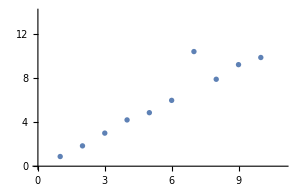

```mathematica
a1=ListPlot[listfit,PlotRange->{{0,11},{0,14}},ImageSize->300]
```

13. Adding a number of formatting options to the chart above

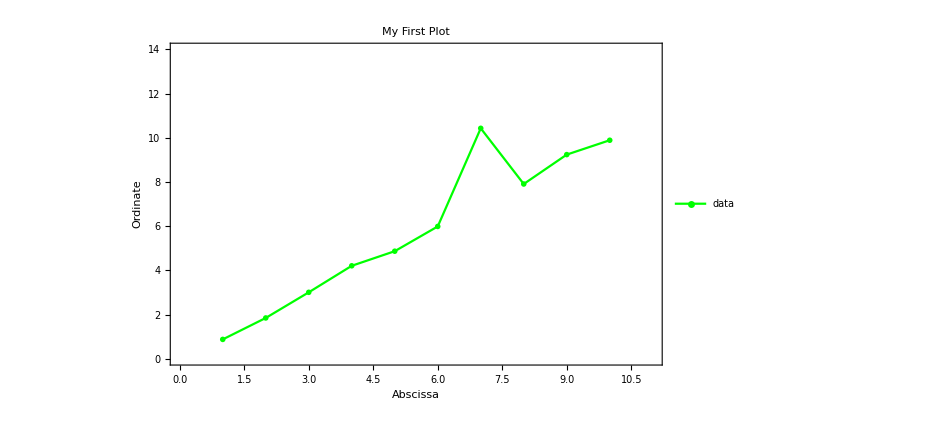

```mathematica
a1=ListPlot[listfit,PlotRange->{{0,11},{0,14}},Frame->True,Joined->True,FrameLabel->{Style["Abscissa",Black,30],Style["Ordinate",Red,30]},FrameTicksStyle->Directive[Black,24],PlotMarkers->{"⋆",24},PlotStyle->Green,PlotLegends->Placed[{"data"},{0.15,0.85}],PlotLabel->Style["My First Plot",Orange,40],ImageSize->700]
```

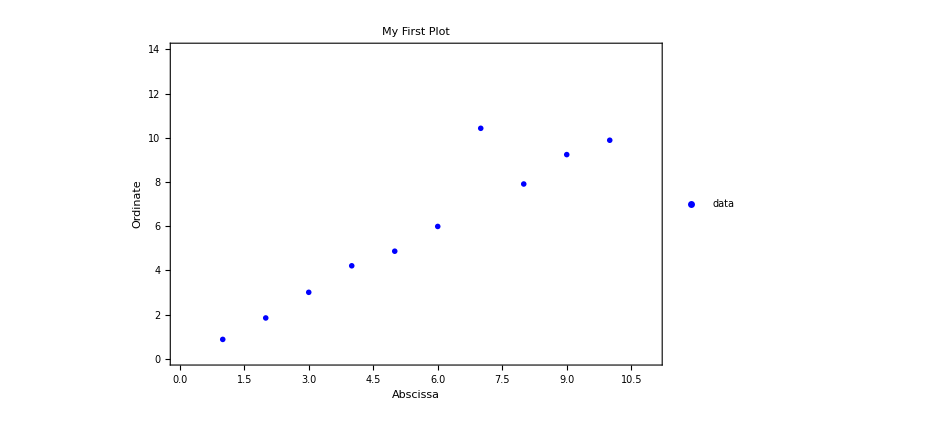

```mathematica
ListPlot[listfit,PlotRange->{{0,11},{0,14}},Frame->True,Joined->False,FrameLabel->{Style["Abscissa",Black,30],Style["Ordinate",Red,30]},FrameTicksStyle->Directive[Black,24],PlotMarkers->{"⋆",24},PlotStyle->Blue,PlotLegends->Placed[{"data"},{0.15,0.85}],PlotLabel->Style["My First Plot",Orange,40],ImageSize->700]
```

16. Now plotting the linear fit generated above

```mathematica
y[x_]:=-0.07533333333333295+1.073333333333333* x
```

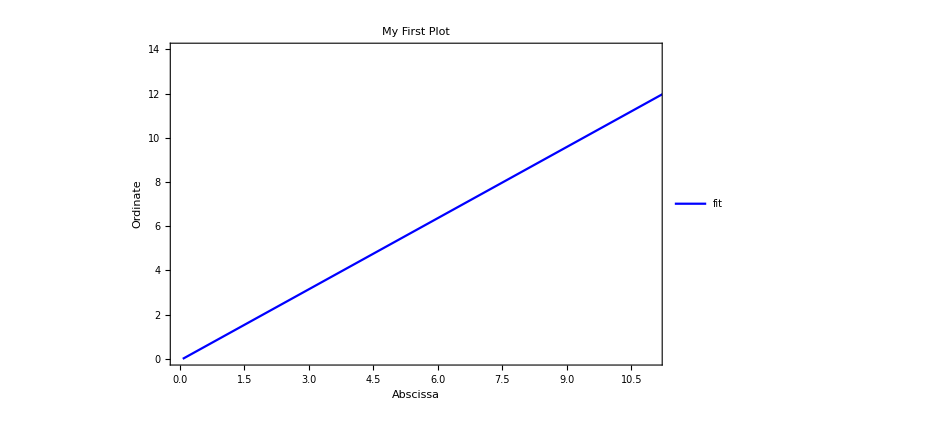

```mathematica
a2=Plot[y[x],{x,0,100},PlotRange->{{0,11},{0,14}},Frame->True,FrameLabel->{Style["Abscissa",Black,30],Style["Ordinate",Red,30]},FrameTicksStyle->Directive[Black,24],PlotStyle->Blue,PlotLegends->Placed[{"fit"},{0.15,0.85}],PlotLabel->Style["My First Plot",Orange,40],ImageSize->700]
```

17. Combining the two plots generated so far (raw data plus linear fit)

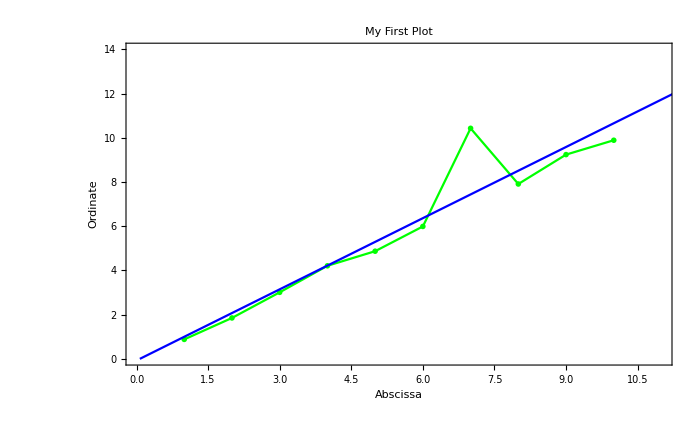

```mathematica
Show[a1,a2]
```

C. Fitting data that has associated error

20. Input of data provided in the lab in the form of (value, error) pairs

```mathematica
listerrorplot={{0.88,0.5},{1.85,0.5},{3.01,0.5},{4.21,0.5},{4.87,0.5},{5.99,0.5},{10.43,3},{7.91,0.5},{9.24,0.5},{9.89,0.5}};
```

21. Importing the tools needed to generate an error bar plot

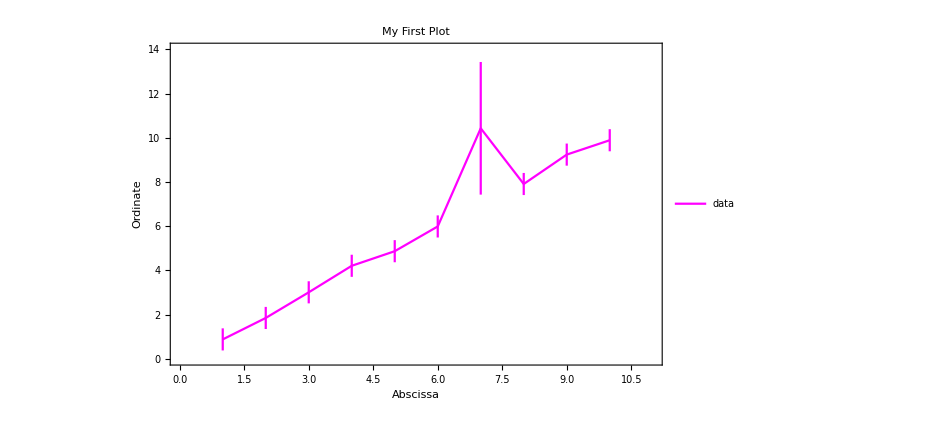

```mathematica
Needs["ErrorBarPlots`"]
tickSpecs={{{1,"1"},{2,"2"},{3,"3"},{4,"4"},{5,"5"},{6,"6"},{7,"7"},{8,"8"},{9,"9"},{10, "10"}}, Automatic};
a3=ErrorListPlot[listerrorplot,PlotRange->{{0,11},{0,14}},Frame -> True,Joined->True,FrameLabel->{Style["Abscissa",Black,30],Style["Ordinate",Red,30]},FrameTicksStyle-> Directive[Black,24],PlotStyle->Magenta,PlotLegends->Placed[{"data"},{0.15,0.85}],PlotLabel->Style["My First Plot",Orange,40],ImageSize->700]
```

This could certainly have done without the connecting lines (i.e. Joined -> False)

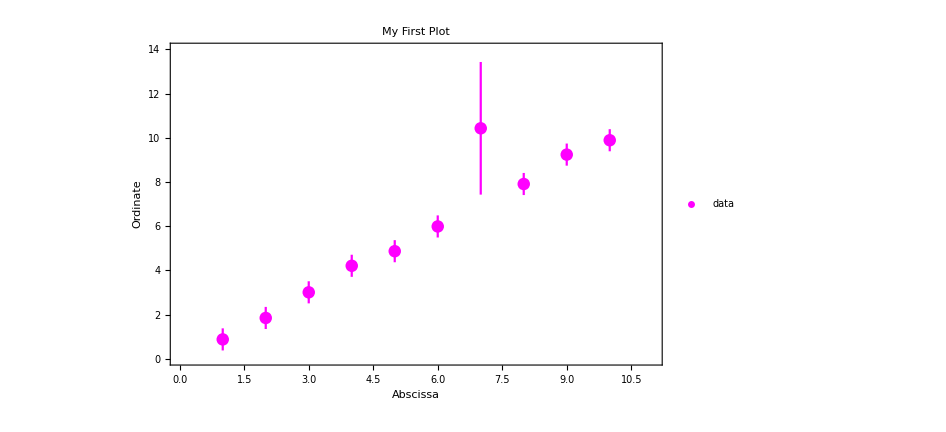

```mathematica
ErrorListPlot[listerrorplot,PlotRange->{{0,11},{0,14}},Frame -> True,FrameLabel->{Style["Abscissa",Black,30],Style["Ordinate",Red,30]},FrameTicksStyle-> Directive[Black,24],PlotStyle->Magenta,PlotLegends->Placed[{"data"},{0.15,0.85}],PlotLabel->Style["My First Plot",Orange,40],ImageSize->700]
```

```mathematica
22. Next we fit the data again, but this time weighting the values using the
 error bars plotted above. In this case each point will be weighted by (1/2)^2
```

```mathematica
f=NonlinearModelFit[listfit,a+b*x,{a,b},x,Weights-> 1/listerrorplot[[All,2]]^2]
```

FittedModel[-0.0753333+1.01298 x]

```mathematica
y2[x_]:=-0.07533333333333216+1.0129759846301634 x;
```

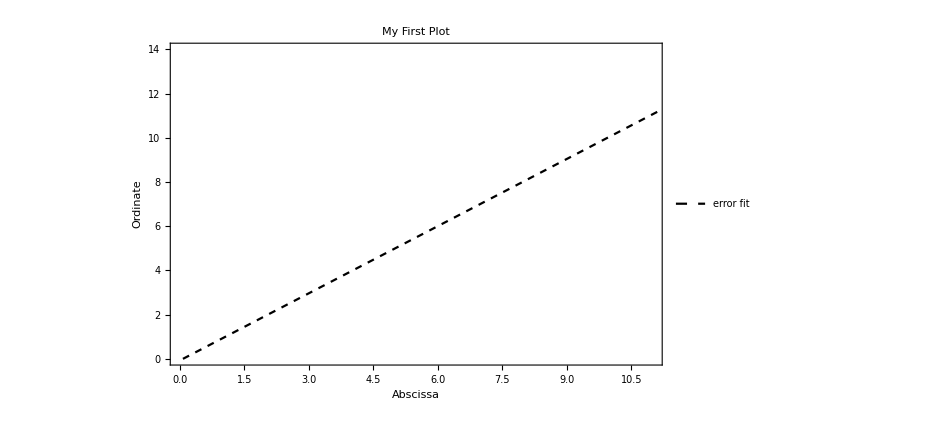

```mathematica
a4=Plot[y2[x],{x,0,100},PlotRange->{{0,11},{0,14}},Frame->True,FrameLabel->{Style["Abscissa",Black,30],Style["Ordinate",Red,30]},FrameTicksStyle->Directive[Black,24],PlotStyle->{Black,Dashed},PlotLegends->Placed[{"error fit"},{0.15,0.85}],PlotLabel->Style["My First Plot",Orange,40],ImageSize->700]
```

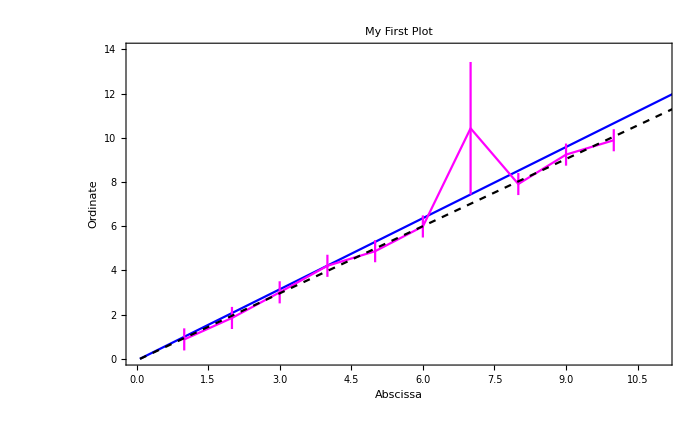

```mathematica
Show[a2,a3,a4]
```